```mathematica
G[A_,B_,α_]:=(
Subscript[n, 1]=Length[A];
Subscript[n, 2]=Length[B];
g=1/(Subscript[n, 1] Subscript[n, 2])Sum[Norm[A[[i]]-B[[j]]]^α,{i,1,Subscript[n, 1]},{j,1,Subscript[n, 2]}];
Return[g];
)

Energy[A_,B_,α_]:=(
Subscript[n, 1]=Length[A];
Subscript[n, 2]=Length[B];
e=(Subscript[n, 1] Subscript[n, 2])/(Subscript[n, 1]+Subscript[n, 2])(2G[A,B,α]-G[A,A,α]-G[B,B,α]);
Return[e];
)

EnergyShuffle[A_,B_,n_]:=(
X1=Join[RandomSample[A,300-n],RandomSample[B,n]];
Y1=Join[RandomSample[B,300-n],RandomSample[A,n]];
Return[Energy[X1,Y1,1]];
)

J[A_,B_]:=(
Subscript[m, a]=Mean[A];
Subscript[m, b]= Mean[B];
Subscript[n, a]=Length[A];
Subscript[n, b]=Length[B];
j=1/2(Sum[Norm[A[[i]]-Subscript[m, a]]^2,{i,1,Length[A]}]+Sum[Norm[B[[i]]-Subscript[m, b]]^2,{i,1,Length[B]}]);
Return[j];
)

KmeansShuffle[A_,B_,n_]:=(
X1=Join[RandomSample[A,300-n],RandomSample[B,n]];
Y1=Join[RandomSample[B,300-n],RandomSample[A,n]];
Return[J[X1,Y1]];
)

GMM[A_,B_]:=(
Subscript[n, a]=Length[A];
Subscript[n, b]=Length[B];
Subscript[μ, a]=Mean[A];
Subscript[μ, b]=Mean[B];
Subscript[Σ, a]=Covariance[A];
Subscript[Σ, b]=Covariance[B];
l=Sum[Log[PDF[MultinormalDistribution[Subscript[μ, a],Subscript[Σ, a]],A[[n]]]],{n,1,Subscript[n, a]}]+Sum[Log[PDF[MultinormalDistribution[Subscript[μ, b],Subscript[Σ, b]],B[[n]]]],{n,1,Subscript[n, b]}];
Return[l];
)

GMMShuffle[A_,B_,n_]:=(
X1=Join[RandomSample[A,300-n],RandomSample[B,n]];
Y1=Join[RandomSample[B,300-n],RandomSample[A,n]];
Return[GMM[X1,Y1]];
)
```

```mathematica
X=RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,2}}],500];
Y=RandomVariate[MultinormalDistribution[{5,5},{{1,0},{0,1}}],500];
```

```mathematica
g1=ListPlot[{X,Y},AspectRatio->1];
g2=ListPlot[Table[{n,EnergyShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->Blue];
g3=ListPlot[Table[{n,KmeansShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->Red];
g4=ListPlot[Table[{n,GMMShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->Darker[Green]];
```

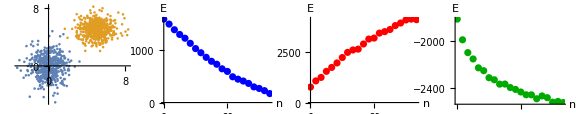

```mathematica
GraphicsGrid[{{g1,g2,g3,g4}},ImageSize->Large]
```

```mathematica
X=RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}],500];
Y=RandomVariate[MultinormalDistribution[{0.5,0},{{2,1},{1,5}}],500];
```

```mathematica
g5=ListPlot[{X,Y},AspectRatio->1];
g6=ListPlot[Table[{n,EnergyShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->Blue];
g7=ListPlot[Table[{n,KmeansShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->Red];
g8=ListPlot[Table[{n,GMMShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->Darker[Green]];
```

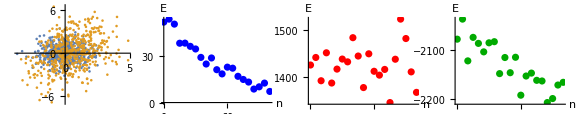

```mathematica
GraphicsGrid[{{g5,g6,g7,g8}},ImageSize->Large]
```

```mathematica
G1[η_]:=(
t = RandomReal[{-1,1}];
v={10t,10 t^3+2 t^2-10t};
v=v+η RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}]];
Return[v];
)
G2[η_]:=(
t = RandomReal[{0,4Pi}];
v={t Cos[t],t Sin[t]};
v=v+η RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}]];
Return[v];
)
G3[η_]:=(
t = RandomReal[{0,4Pi}];
v={3 Cos[t],3 Sin[t],3t};
v=v+η RandomVariate[MultinormalDistribution[{0,0,0},{{1,0,0},{0,1,0},{0,0,1}}]];
Return[v];
)

G4[η_]:=(
t = RandomReal[{-1,1}];
v={10t+12,10 t^3+2 t^2-10t+1};
v=v+η RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}]];
Return[v];
)
G5[η_]:=(
t = RandomReal[{0,4Pi}];
v={-t Cos[t],-t Sin[t]};
v=v+η RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}]];
Return[v];
)
G6[η_]:=(
t = RandomReal[{0,4Pi}];
v={-Cos[t],- Sin[t],2t};
v=v+η RandomVariate[MultinormalDistribution[{0,0,0},{{1,0,0},{0,1,0},{0,0,1}}]];
Return[v];
)
```

```mathematica
GraphicsRow[{
ListPlot[{Table[G1[0.1],{i,1,400}],Table[G4[0.1],{i,1,400}]}],
ListPlot[{Table[G2[0.1],{i,1,500}],Table[G5[0.1],{i,1,500}]}],
ListPointPlot3D[{Table[G3[0.05],{i,1,400}],Table[G6[0.05],{i,1,400}]}]},ImageSize->Large]
```

-Graphics-

```mathematica
X=Table[G1[0.1],{i,1,500}];
Y=Table[G4[0.1],{i,1,500}];
```

```mathematica
g9=ListPlot[{X,Y},AspectRatio->1];
g10=ListPlot[Table[{n,EnergyShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->Blue];
g11=ListPlot[Table[{n,KmeansShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->Red];
g12=ListPlot[Table[{n,GMMShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->Darker[Green]];
```

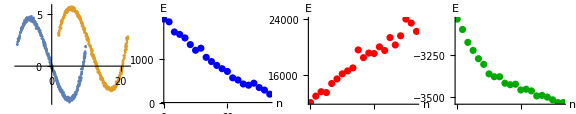

```mathematica
GraphicsGrid[{{g9,g10,g11,g12}},ImageSize->Large]
```

```mathematica
X=Table[G2[0.1],{i,1,500}];
Y=Table[G5[0.1],{i,1,500}];
```

```mathematica
g13=ListPlot[{X,Y},AspectRatio->1];
g14=ListPlot[Table[{n,EnergyShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->Blue];
g15=ListPlot[Table[{n,KmeansShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->Red];
g16=ListPlot[Table[{n,GMMShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->Darker[Green]];
```

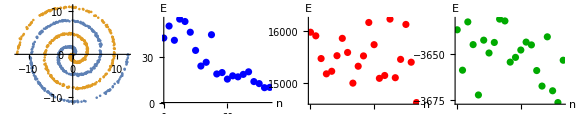

```mathematica
GraphicsGrid[{{g13,g14,g15,g16}},ImageSize->Large]
```

```mathematica
X=Table[G3[0.05],{i,1,500}];
Y=Table[G6[0.05],{i,1,500}];
```

```mathematica
g17=ListPointPlot3D[{X,Y},AspectRatio->1];
g18=ListPlot[Table[{n,EnergyShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->{Blue,PointSize[Medium]}];
g19=ListPlot[Table[{n,KmeansShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->{Red,PointSize[Medium]}];
g20=ListPlot[Table[{n,GMMShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->{Darker[Green],PointSize[Medium]}];
```

```mathematica
GraphicsGrid[{{g17,g18,g19,g20}},ImageSize->Large]
```

-Graphics-

```mathematica
g=GraphicsGrid[{
{g1,g2,g3,g4},
{g5,g6,g7,g8},
{g9,g10,g11,g12},
{g13,g14,g15,g16},
{g17,g18,g19,g20}
},ImageSize->900]
```

-Graphics-

```mathematica
Export["C:\\Users\\guifr\\Desktop\\energy_kmeans_gmm.pdf",g,"PDF"]
```

C:\Users\guifr\Desktop\energy_kmeans_gmm.pdf

```mathematica
K=Table[Subscript[A, i,j],{i,1,5},{j,1,5}];
Z={{1,1,0,0,0},{0,0,1,1,0},{0,0,0,0,1}};
M[k_]:=Sum[Z[[k,l]],{l,1,5}]
S1[i_]:=K[[i,i]]
S2[k_,i_]:=Sum[Z[[k,l]]K[[i,l]],{l,1,5}]
S3[k_]:=Sum[Z[[k,l]]Z[[k,p]]K[[l,p]],{l,1,5},{p,1,5}]
K//MatrixForm
Z//MatrixForm
```

(A_(1,1) | A_(1,2) | A_(1,3) | A_(1,4) | A_(1,5)
A_(2,1) | A_(2,2) | A_(2,3) | A_(2,4) | A_(2,5)
A_(3,1) | A_(3,2) | A_(3,3) | A_(3,4) | A_(3,5)
A_(4,1) | A_(4,2) | A_(4,3) | A_(4,4) | A_(4,5)
A_(5,1) | A_(5,2) | A_(5,3) | A_(5,4) | A_(5,5))

(1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
S3[1]
```

A_(1,1)+A_(1,2)+A_(2,1)+A_(2,2)

```mathematica
1/2Sum[Z[[k,i]](S1[i]-2/M[k] S2[k,i]+1/M[k]^2 S3[k]),{k,1,3},{i,1,5}]/.{Subscript[A, 2,1]->Subscript[A, 1,2],Subscript[A, 4,3]->Subscript[A, 3,4]}//FullSimplify
```

1/4 (A_(1,1)-2 A_(1,2)+A_(2,2)+A_(3,3)-2 A_(3,4)+A_(4,4))

```mathematica
Z.K.Transpose[Z]//MatrixForm
```

(A_(1,1)+A_(1,2)+A_(2,1)+A_(2,2) | A_(1,3)+A_(1,4)+A_(2,3)+A_(2,4) | A_(1,5)+A_(2,5)
A_(3,1)+A_(3,2)+A_(4,1)+A_(4,2) | A_(3,3)+A_(3,4)+A_(4,3)+A_(4,4) | A_(3,5)+A_(4,5)
A_(5,1)+A_(5,2) | A_(5,3)+A_(5,4) | A_(5,5))

```mathematica
Z[[1,1]]K[[1,1]]
```

k_(1,1)

```mathematica
Sum[Z[[1,l]]K[[1,l]],{l,1,5}]
```

k_(1,1)+k_(1,2)